# Метод на Ойлер за решаване задача на Коши с начално условие

## Задача от лекции

y’ = x+1/y, x ∈ [0,1]
y(0) = 2

### Търсим точно решение

търсим общо решение:

```mathematica
DSolve[y'[x]== x + 1/y[x], y[x],x]
```

Solve[((-1)^(2/3) 2^(1/3) x AiryAi[-1/2 (-1/2)^(1/3) (x^2-2 y[x])]-2 AiryAiPrime[-1/2 (-1/2)^(1/3) (x^2-2 y[x])])/((-1)^(2/3) 2^(1/3) x AiryBi[-1/2 (-1/2)^(1/3) (x^2-2 y[x])]-2 AiryBiPrime[-1/2 (-1/2)^(1/3) (x^2-2 y[x])])+C[1]==0,y[x]]

търсим частно решение:

```mathematica
DSolve[{y'[x]== x + 1/y[x], y[0] == 2}, y[x],x]
```

Solve[-AiryAiPrime[(-1)^(1/3) 2^(2/3)]/AiryBiPrime[(-1)^(1/3) 2^(2/3)]+((-1)^(2/3) 2^(1/3) x AiryAi[-1/2 (-1/2)^(1/3) (x^2-2 y[x])]-2 AiryAiPrime[-1/2 (-1/2)^(1/3) (x^2-2 y[x])])/((-1)^(2/3) 2^(1/3) x AiryBi[-1/2 (-1/2)^(1/3) (x^2-2 y[x])]-2 AiryBiPrime[-1/2 (-1/2)^(1/3) (x^2-2 y[x])])==0,y[x]]

Извод: Не можем да намерим точно решение с аналитичен метод

### Търсим приближено (числено) решение

```mathematica
(*въвеждаме условието на задачата*)
a = 0.; b = 1;
x = a;
y = 2.;
f[x_,y_]:=x+1/y
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y]];
y = y+h*f[x,y];
x=x+h
]
```

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.0625

Теоретичната глобална грешка е 0.25

i = 0 x_i = 0. y_i = 2. f_i = 0.5

i = 1 x_i = 0.25 y_i = 2.125 f_i = 0.720588

i = 2 x_i = 0.5 y_i = 2.30515 f_i = 0.933812

i = 3 x_i = 0.75 y_i = 2.5386 f_i = 1.14392

i = 4 x_i = 1. y_i = 2.82458 f_i = 1.35404

## Задача 3 a) от файла

y’ = y/x+1, x ∈ [1,2]
y(1) = 0

### Търсим точно решение

търсим общо решение:

```mathematica
Clear[x,y]
DSolve[y'[x]== y[x]/x+1, y[x],x]
```

{{y[x]→x C[1]+x Log[x]}}

търсим частно решение:

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x]/x+1, y[1] == 0}, y[x],x]
```

{{y[x]→x Log[x]}}

визуализация на точното решение

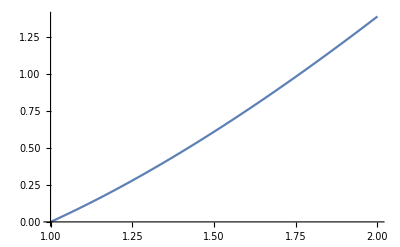

```mathematica
yt[x_]:=x Log[x]
Plot[yt[x],{x,1,2}]
```

Извод: Не можем да намерим точно решение с аналитичен метод

### Търсим приближено (числено) решение

#### n = 4

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.0625

Теоретичната глобална грешка е 0.25

i = 0 x_i = 1. y_i = 0. f_i = 1. y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.25 f_i = 1.2 y_точно = 0.278929 истинска грешка = 0.0289294

i = 2 x_i = 1.5 y_i = 0.55 f_i = 1.36667 y_точно = 0.608198 истинска грешка = 0.0581977

i = 3 x_i = 1.75 y_i = 0.891667 f_i = 1.50952 y_точно = 0.979328 истинска грешка = 0.087661

i = 4 x_i = 2. y_i = 1.26905 f_i = 1.63452 y_точно = 1.38629 истинска грешка = 0.117247

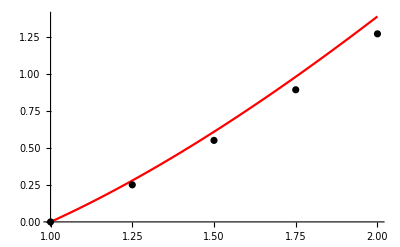

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x,y];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### n = 10

Мрежата е с n = 10 и стъпка h = 0.1

Теоретичната локална  грешка е 0.01

Теоретичната глобална грешка е 0.1

i = 0 x_i = 1. y_i = 0. f_i = 1. y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.1 y_i = 0.1 f_i = 1.09091 y_точно = 0.104841 истинска грешка = 0.0048412

i = 2 x_i = 1.2 y_i = 0.209091 f_i = 1.17424 y_точно = 0.218786 истинска грешка = 0.00969496

i = 3 x_i = 1.3 y_i = 0.326515 f_i = 1.25117 y_точно = 0.341074 истинска грешка = 0.0145584

i = 4 x_i = 1.4 y_i = 0.451632 f_i = 1.32259 y_точно = 0.471061 истинска грешка = 0.0194294

i = 5 x_i = 1.5 y_i = 0.583891 f_i = 1.38926 y_точно = 0.608198 истинска грешка = 0.0243066

i = 6 x_i = 1.6 y_i = 0.722817 f_i = 1.45176 y_точно = 0.752006 истинска грешка = 0.0291886

i = 7 x_i = 1.7 y_i = 0.867993 f_i = 1.51058 y_точно = 0.902068 истинска грешка = 0.0340748

i = 8 x_i = 1.8 y_i = 1.01905 f_i = 1.56614 y_точно = 1.05802 истинска грешка = 0.0389643

i = 9 x_i = 1.9 y_i = 1.17567 f_i = 1.61877 y_точно = 1.21952 истинска грешка = 0.0438567

i = 10 x_i = 2. y_i = 1.33754 f_i = 1.66877 y_точно = 1.38629 истинска грешка = 0.0487516

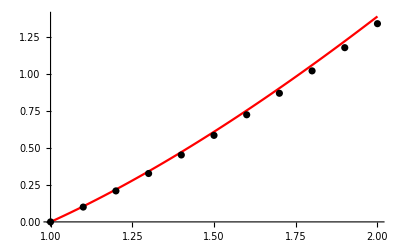

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 10; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x,y];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### n = 100

Мрежата е с n = 100 и стъпка h = 0.01

Теоретичната локална  грешка е 0.0001

Теоретичната глобална грешка е 0.01

i = 0 x_i = 1. y_i = 0. f_i = 1. y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.01 y_i = 0.01 f_i = 1.0099 y_точно = 0.0100498 истинска грешка = 0.0000498342

i = 2 x_i = 1.02 y_i = 0.020099 f_i = 1.0197 y_точно = 0.0201987 истинска грешка = 0.0000996699

i = 3 x_i = 1.03 y_i = 0.0302961 f_i = 1.02941 y_точно = 0.0304456 истинска грешка = 0.000149507

i = 4 x_i = 1.04 y_i = 0.0405902 f_i = 1.03903 y_точно = 0.0407895 истинска грешка = 0.000199346

i = 5 x_i = 1.05 y_i = 0.0509805 f_i = 1.04855 y_точно = 0.0512297 истинска грешка = 0.000249187

i = 6 x_i = 1.06 y_i = 0.061466 f_i = 1.05799 y_точно = 0.061765 истинска грешка = 0.000299028

i = 7 x_i = 1.07 y_i = 0.0720459 f_i = 1.06733 y_точно = 0.0723948 истинска грешка = 0.000348872

i = 8 x_i = 1.08 y_i = 0.0827192 f_i = 1.07659 y_точно = 0.0831179 истинска грешка = 0.000398716

i = 9 x_i = 1.09 y_i = 0.0934851 f_i = 1.08577 y_точно = 0.0939337 истинска грешка = 0.000448562

i = 10 x_i = 1.1 y_i = 0.104343 f_i = 1.09486 y_точно = 0.104841 истинска грешка = 0.000498409

i = 11 x_i = 1.11 y_i = 0.115291 f_i = 1.10387 y_точно = 0.11584 истинска грешка = 0.000548258

i = 12 x_i = 1.12 y_i = 0.12633 f_i = 1.11279 y_точно = 0.126928 истинска грешка = 0.000598107

i = 13 x_i = 1.13 y_i = 0.137458 f_i = 1.12164 y_точно = 0.138106 истинска грешка = 0.000647958

i = 14 x_i = 1.14 y_i = 0.148674 f_i = 1.13042 y_точно = 0.149372 истинска грешка = 0.00069781

i = 15 x_i = 1.15 y_i = 0.159979 f_i = 1.13911 y_точно = 0.160726 истинска грешка = 0.000747663

i = 16 x_i = 1.16 y_i = 0.17137 f_i = 1.14773 y_точно = 0.172167 истинска грешка = 0.000797517

i = 17 x_i = 1.17 y_i = 0.182847 f_i = 1.15628 y_точно = 0.183694 истинска грешка = 0.000847373

i = 18 x_i = 1.18 y_i = 0.19441 f_i = 1.16475 y_точно = 0.195307 истинска грешка = 0.000897229

i = 19 x_i = 1.19 y_i = 0.206057 f_i = 1.17316 y_точно = 0.207004 истинска грешка = 0.000947086

i = 20 x_i = 1.2 y_i = 0.217789 f_i = 1.18149 y_точно = 0.218786 истинска грешка = 0.000996944

i = 21 x_i = 1.21 y_i = 0.229604 f_i = 1.18976 y_точно = 0.230651 истинска грешка = 0.0010468

i = 22 x_i = 1.22 y_i = 0.241501 f_i = 1.19795 y_точно = 0.242598 истинска грешка = 0.00109666

i = 23 x_i = 1.23 y_i = 0.253481 f_i = 1.20608 y_точно = 0.254627 истинска грешка = 0.00114653

i = 24 x_i = 1.24 y_i = 0.265542 f_i = 1.21415 y_точно = 0.266738 истинска грешка = 0.00119639

i = 25 x_i = 1.25 y_i = 0.277683 f_i = 1.22215 y_точно = 0.278929 истинска грешка = 0.00124625

i = 26 x_i = 1.26 y_i = 0.289905 f_i = 1.23008 y_точно = 0.291201 истинска грешка = 0.00129611

i = 27 x_i = 1.27 y_i = 0.302205 f_i = 1.23796 y_точно = 0.303551 истинска грешка = 0.00134598

i = 28 x_i = 1.28 y_i = 0.314585 f_i = 1.24577 y_точно = 0.315981 истинска грешка = 0.00139584

i = 29 x_i = 1.29 y_i = 0.327043 f_i = 1.25352 y_точно = 0.328488 истинска грешка = 0.00144571

i = 30 x_i = 1.3 y_i = 0.339578 f_i = 1.26121 y_точно = 0.341074 истинска грешка = 0.00149558

i = 31 x_i = 1.31 y_i = 0.35219 f_i = 1.26885 y_точно = 0.353736 истинска грешка = 0.00154544

i = 32 x_i = 1.32 y_i = 0.364879 f_i = 1.27642 y_точно = 0.366474 истинска грешка = 0.00159531

i = 33 x_i = 1.33 y_i = 0.377643 f_i = 1.28394 y_точно = 0.379288 истинска грешка = 0.00164518

i = 34 x_i = 1.34 y_i = 0.390482 f_i = 1.2914 y_точно = 0.392177 истинска грешка = 0.00169505

i = 35 x_i = 1.35 y_i = 0.403396 f_i = 1.29881 y_точно = 0.405141 истинска грешка = 0.00174492

i = 36 x_i = 1.36 y_i = 0.416384 f_i = 1.30616 y_точно = 0.418179 истинска грешка = 0.00179479

i = 37 x_i = 1.37 y_i = 0.429446 f_i = 1.31346 y_точно = 0.431291 истинска грешка = 0.00184467

i = 38 x_i = 1.38 y_i = 0.442581 f_i = 1.32071 y_точно = 0.444475 истинска грешка = 0.00189454

i = 39 x_i = 1.39 y_i = 0.455788 f_i = 1.3279 y_точно = 0.457732 истинска грешка = 0.00194441

i = 40 x_i = 1.4 y_i = 0.469067 f_i = 1.33505 y_точно = 0.471061 истинска грешка = 0.00199429

i = 41 x_i = 1.41 y_i = 0.482417 f_i = 1.34214 y_точно = 0.484461 истинска грешка = 0.00204416

i = 42 x_i = 1.42 y_i = 0.495839 f_i = 1.34918 y_точно = 0.497933 истинска грешка = 0.00209404

i = 43 x_i = 1.43 y_i = 0.509331 f_i = 1.35618 y_точно = 0.511474 истинска грешка = 0.00214391

i = 44 x_i = 1.44 y_i = 0.522892 f_i = 1.36312 y_точно = 0.525086 истинска грешка = 0.00219379

i = 45 x_i = 1.45 y_i = 0.536523 f_i = 1.37002 y_точно = 0.538767 истинска грешка = 0.00224366

i = 46 x_i = 1.46 y_i = 0.550224 f_i = 1.37687 y_точно = 0.552517 истинска грешка = 0.00229354

i = 47 x_i = 1.47 y_i = 0.563992 f_i = 1.38367 y_точно = 0.566336 истинска грешка = 0.00234342

i = 48 x_i = 1.48 y_i = 0.577829 f_i = 1.39042 y_точно = 0.580222 истинска грешка = 0.0023933

i = 49 x_i = 1.49 y_i = 0.591733 f_i = 1.39714 y_точно = 0.594176 истинска грешка = 0.00244318

i = 50 x_i = 1.5 y_i = 0.605705 f_i = 1.4038 y_точно = 0.608198 истинска грешка = 0.00249306

i = 51 x_i = 1.51 y_i = 0.619743 f_i = 1.41043 y_точно = 0.622286 истинска грешка = 0.00254294

i = 52 x_i = 1.52 y_i = 0.633847 f_i = 1.417 y_точно = 0.63644 истинска грешка = 0.00259282

i = 53 x_i = 1.53 y_i = 0.648017 f_i = 1.42354 y_точно = 0.65066 истинска грешка = 0.0026427

i = 54 x_i = 1.54 y_i = 0.662252 f_i = 1.43003 y_точно = 0.664945 истинска грешка = 0.00269258

i = 55 x_i = 1.55 y_i = 0.676553 f_i = 1.43649 y_точно = 0.679295 истинска грешка = 0.00274246

i = 56 x_i = 1.56 y_i = 0.690918 f_i = 1.4429 y_точно = 0.69371 истинска грешка = 0.00279234

i = 57 x_i = 1.57 y_i = 0.705346 f_i = 1.44927 y_точно = 0.708189 истинска грешка = 0.00284222

i = 58 x_i = 1.58 y_i = 0.719839 f_i = 1.45559 y_точно = 0.722731 истинска грешка = 0.00289211

i = 59 x_i = 1.59 y_i = 0.734395 f_i = 1.46188 y_точно = 0.737337 истинска грешка = 0.00294199

i = 60 x_i = 1.6 y_i = 0.749014 f_i = 1.46813 y_точно = 0.752006 истинска грешка = 0.00299188

i = 61 x_i = 1.61 y_i = 0.763695 f_i = 1.47434 y_точно = 0.766737 истинска грешка = 0.00304176

i = 62 x_i = 1.62 y_i = 0.778439 f_i = 1.48052 y_точно = 0.78153 истинска грешка = 0.00309164

i = 63 x_i = 1.63 y_i = 0.793244 f_i = 1.48665 y_точно = 0.796385 истинска грешка = 0.00314153

i = 64 x_i = 1.64 y_i = 0.80811 f_i = 1.49275 y_точно = 0.811302 истинска грешка = 0.00319141

i = 65 x_i = 1.65 y_i = 0.823038 f_i = 1.49881 y_точно = 0.826279 истинска грешка = 0.0032413

i = 66 x_i = 1.66 y_i = 0.838026 f_i = 1.50483 y_точно = 0.841317 истинска грешка = 0.00329119

i = 67 x_i = 1.67 y_i = 0.853074 f_i = 1.51082 y_точно = 0.856415 истинска грешка = 0.00334107

i = 68 x_i = 1.68 y_i = 0.868183 f_i = 1.51678 y_точно = 0.871574 истинска грешка = 0.00339096

i = 69 x_i = 1.69 y_i = 0.88335 f_i = 1.52269 y_точно = 0.886791 истинска грешка = 0.00344085

i = 70 x_i = 1.7 y_i = 0.898577 f_i = 1.52857 y_точно = 0.902068 истинска грешка = 0.00349074

i = 71 x_i = 1.71 y_i = 0.913863 f_i = 1.53442 y_точно = 0.917404 истинска грешка = 0.00354062

i = 72 x_i = 1.72 y_i = 0.929207 f_i = 1.54024 y_точно = 0.932798 истинска грешка = 0.00359051

i = 73 x_i = 1.73 y_i = 0.94461 f_i = 1.54602 y_точно = 0.94825 истинска грешка = 0.0036404

i = 74 x_i = 1.74 y_i = 0.96007 f_i = 1.55176 y_точно = 0.96376 истинска грешка = 0.00369029

i = 75 x_i = 1.75 y_i = 0.975587 f_i = 1.55748 y_точно = 0.979328 истинска грешка = 0.00374018

i = 76 x_i = 1.76 y_i = 0.991162 f_i = 1.56316 y_точно = 0.994952 истинска грешка = 0.00379007

i = 77 x_i = 1.77 y_i = 1.00679 f_i = 1.56881 y_точно = 1.01063 истинска грешка = 0.00383996

i = 78 x_i = 1.78 y_i = 1.02248 f_i = 1.57443 y_точно = 1.02637 истинска грешка = 0.00388985

i = 79 x_i = 1.79 y_i = 1.03823 f_i = 1.58001 y_точно = 1.04217 истинска грешка = 0.00393974

i = 80 x_i = 1.8 y_i = 1.05403 f_i = 1.58557 y_точно = 1.05802 истинска грешка = 0.00398963

i = 81 x_i = 1.81 y_i = 1.06988 f_i = 1.5911 y_точно = 1.07392 истинска грешка = 0.00403952

i = 82 x_i = 1.82 y_i = 1.08579 f_i = 1.59659 y_точно = 1.08988 истинска грешка = 0.00408941

i = 83 x_i = 1.83 y_i = 1.10176 f_i = 1.60205 y_точно = 1.1059 истинска грешка = 0.0041393

i = 84 x_i = 1.84 y_i = 1.11778 f_i = 1.60749 y_точно = 1.12197 истинска грешка = 0.0041892

i = 85 x_i = 1.85 y_i = 1.13385 f_i = 1.61289 y_точно = 1.13809 истинска грешка = 0.00423909

i = 86 x_i = 1.86 y_i = 1.14998 f_i = 1.61827 y_точно = 1.15427 истинска грешка = 0.00428898

i = 87 x_i = 1.87 y_i = 1.16617 f_i = 1.62362 y_точно = 1.1705 истинска грешка = 0.00433887

i = 88 x_i = 1.88 y_i = 1.1824 f_i = 1.62894 y_точно = 1.18679 истинска грешка = 0.00438877

i = 89 x_i = 1.89 y_i = 1.19869 f_i = 1.63423 y_точно = 1.20313 истинска грешка = 0.00443866

i = 90 x_i = 1.9 y_i = 1.21503 f_i = 1.63949 y_точно = 1.21952 истинска грешка = 0.00448855

i = 91 x_i = 1.91 y_i = 1.23143 f_i = 1.64473 y_точно = 1.23597 истинска грешка = 0.00453845

i = 92 x_i = 1.92 y_i = 1.24788 f_i = 1.64994 y_точно = 1.25246 истинска грешка = 0.00458834

i = 93 x_i = 1.93 y_i = 1.26438 f_i = 1.65512 y_точно = 1.26901 истинска грешка = 0.00463823

i = 94 x_i = 1.94 y_i = 1.28093 f_i = 1.66027 y_точно = 1.28561 истинска грешка = 0.00468813

i = 95 x_i = 1.95 y_i = 1.29753 f_i = 1.6654 y_точно = 1.30227 истинска грешка = 0.00473802

i = 96 x_i = 1.96 y_i = 1.31418 f_i = 1.6705 y_точно = 1.31897 истинска грешка = 0.00478792

i = 97 x_i = 1.97 y_i = 1.33089 f_i = 1.67558 y_точно = 1.33573 истинска грешка = 0.00483781

i = 98 x_i = 1.98 y_i = 1.34764 f_i = 1.68063 y_точно = 1.35253 истинска грешка = 0.00488771

i = 99 x_i = 1.99 y_i = 1.36445 f_i = 1.68565 y_точно = 1.36939 истинска грешка = 0.0049376

i = 100 x_i = 2. y_i = 1.38131 f_i = 1.69065 y_точно = 1.38629 истинска грешка = 0.0049875

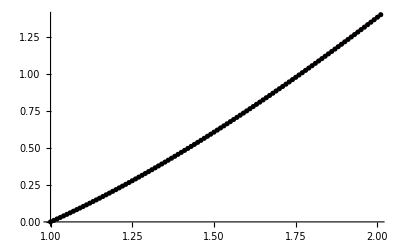

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 100; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x,y];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### При достигане на точност 10^-6

```mathematica
a = 1.; b = 2;
Clear[n]
Reduce[(b-a)/n<= 10^-6,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^6

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 10^6; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
```

Мрежата е с n = 1000000 и стъпка h = 1.×10^-6

Теоретичната локална  грешка е 1.×10^-12

Теоретичната глобална грешка е 1.×10^-6

Извод: След като пуснахме кода ни беше необходимо твърде много време за смятане

# Модифициран метод на Ойлер за решаване задача на Коши с начално условие

#### n = 4

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. f_i = 1. x_(i + 1/2) = 1.125 y_(i + 1/2) = 0.125 f_(i + 1/2) = 1.11111 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.277778 f_i = 1.22222 x_(i + 1/2) = 1.375 y_(i + 1/2) = 0.430556 f_(i + 1/2) = 1.31313 y_точно = 0.278929 истинска грешка = 0.00115166

i = 2 x_i = 1.5 y_i = 0.606061 f_i = 1.40404 x_(i + 1/2) = 1.625 y_(i + 1/2) = 0.781566 f_(i + 1/2) = 1.48096 y_точно = 0.608198 истинска грешка = 0.00213706

i = 3 x_i = 1.75 y_i = 0.976301 f_i = 1.55789 x_(i + 1/2) = 1.875 y_(i + 1/2) = 1.17104 f_(i + 1/2) = 1.62455 y_точно = 0.979328 истинска грешка = 0.00302615

i = 4 x_i = 2. y_i = 1.38244 f_i = 1.69122 x_(i + 1/2) = 2.125 y_(i + 1/2) = 1.59384 f_(i + 1/2) = 1.75004 y_точно = 1.38629 истинска грешка = 0.00385458

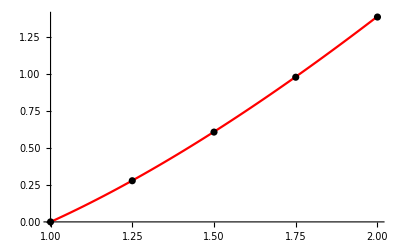

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
x12 = x+h/2;
y12 = y +h/2*f[x,y];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " x_(i + 1/2) = ",x12, " y_(i + 1/2) = ",y12, " f_(i + 1/2) = ",f[x12,y12], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x12,y12];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### При достигане на точност 10^-6

```mathematica
a = 1.; b = 2;
Clear[n]
Reduce[((b-a)/n)^2<= 10^-6,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-1000.||n≥1000.

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 10^3; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 1000 и стъпка h = 0.001

Теоретичната локална  грешка е 1.×10^-9

Теоретичната глобална грешка е 1.×10^-6